```mathematica
(□_□)_□
```

# PRACTICA 2 - 1

## ACTIVIDAD 1

### Diseñe un módulo Mathematica que, tomando como entrada los siguientes parámetros, nos proporcione como salida la simulación del AC unidimensional correspondiente

```mathematica
AC[Inicial_List,Regla_Integer,t_Integer]:=Module[{bi,reglaNum,i,j,resultado,aux,res,actual,long,izq,der,pos,num},
bi = IntegerDigits[Regla,2];
bi = Reverse[bi];
reglaNum ={ {0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1} };

For[i =1,i≤Length[reglaNum],i++,
If [i≤Length[bi], AppendTo[reglaNum[[i]],bi[[i]]];];
If [i>Length[bi], AppendTo[reglaNum[[i]],0];];
];

resultado = {};
aux = {};
res = {};

For[i=1,i≤ Length[Inicial],i++, AppendTo[aux,0];];
For[i=1,i≤ Length[Inicial],i++,AppendTo[res,aux];];

AppendTo[resultado,ArrayPlot[res]];
actual = Inicial;
res = Delete[res,1];
AppendTo[res,actual];
AppendTo[resultado,ArrayPlot[res]];

For[j=1,j≤t,j++,
long = Length[actual]+1;
aux={};
For[i=1,i<long,i++,
izq=Mod[(i-1),long];
pos=i;
der=Mod[(i+1),long];
If[izq==0,izq=9];
If[der==0,der=1];
num=Cases[reglaNum,{actual[[izq]],actual[[pos]],actual[[der]],_}];
AppendTo[aux,num[[1,4]]];
];
res=Delete[res,1];
AppendTo[res,aux];
AppendTo[resultado,ArrayPlot[res]];

actual=aux;
aux={};
];
Print[ListAnimate[resultado]];
Return [resultado];
];
```

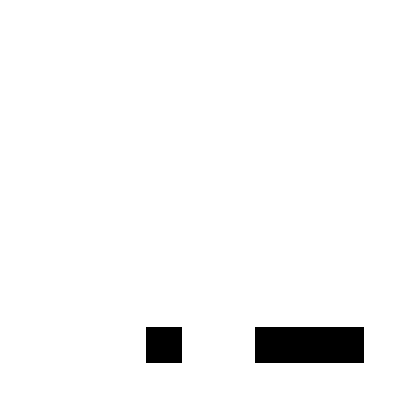
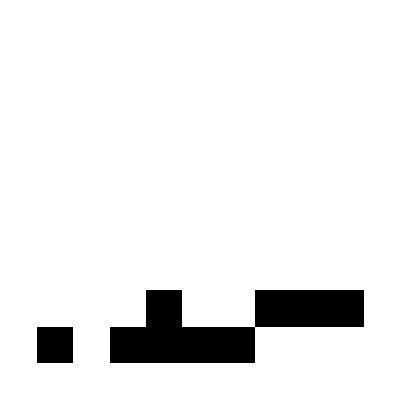
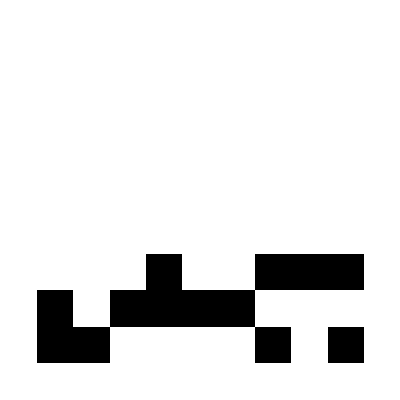
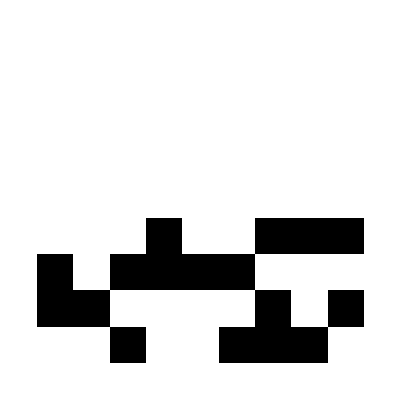
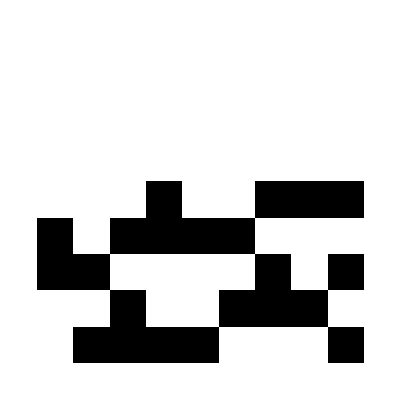
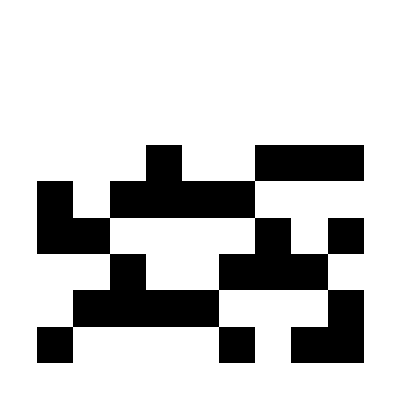
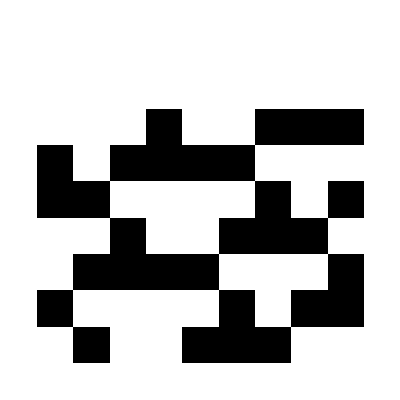
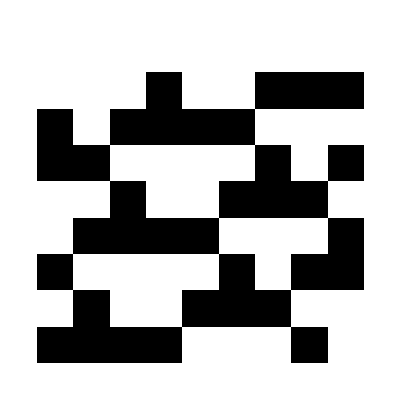
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AC[{0,0,0,1,0,0,1,1,1},54,10]
```